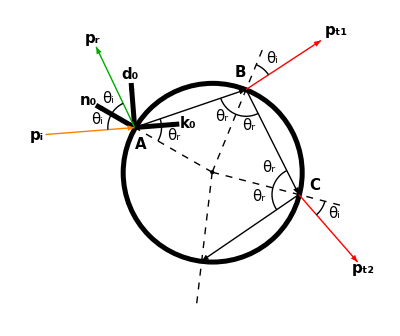

```mathematica
θA = 5Pi/6;
θk0=Pi/40;
nm=1.33;
np=1;
k0={Cos[θk0],Sin[θk0]}//N;
n0={Cos[θA],Sin[θA]}//N;
d0 =(n0-Dot[k0,n0]k0)/Norm[n0-Dot[k0,n0]k0]//N;
θi=ArcCos[-Dot[k0,n0]];
θr=ArcSin[nm Sin[θi]/np];
pA={Cos[θA],Sin[θA]}//N;
pB={Cos[θA-1*(Pi-2 θr)],Sin[θA-1*(Pi-2 θr)]}//N;pC={Cos[θA-2*(Pi-2 θr)],Sin[θA-2*(Pi-2 θr)]}//N;
pD={Cos[θA-3*(Pi-2 θr)],Sin[θA-3*(Pi-2 θr)]}//N;
pr=Re[Exp[-ⅈ 2 θi]]k0+Im[Exp[-ⅈ 2 θi]]d0;
pt[n_]:=Re[Exp[-ⅈ (2 θi+n(Pi-2θr))]]k0+Im[Exp[-ⅈ (2 θi+n(Pi-2θr))]]d0;
Show[
(* circle *)
Graphics[{Thickness[0.009],Circle[{0,0},1]}],
(* point 0 *)
Graphics[{PointSize[Large],Point[{0,0}]}],
(* point A *)
Graphics[{PointSize[Large],Point[pA]}],
Graphics[{Dashed,Line[{{0,0},1.5pA}]}],
Graphics[Text[Style["A",FontSize->15,Bold],pA+0.2{Cos[-1.2],Sin[-1.2]}]],
(* point B *)
Graphics[{PointSize[Large],Point[pB]}],
Graphics[{Dashed,Line[{{0,0},1.5pB}]}],
Graphics[Text[Style["B",FontSize->15,Bold],pB+0.2{Cos[1.9],Sin[1.9]}]],
(* point C *)
Graphics[{PointSize[Large],Point[pC]}],
Graphics[{Dashed,Line[{{0,0},1.5pC}]}],
Graphics[Text[Style["C",FontSize->15,Bold],pC+0.2{Cos[0.5],Sin[0.5]}]],
(* point D *)
Graphics[{PointSize[Large],Point[pD]}],
Graphics[{Dashed,Line[{{0,0},1.5pD}]}],
(* normal *)
Graphics[{Thickness[0.009],Arrow[{n0,1.5n0}]}],
Graphics[Text[Style["n_0",FontSize->15,Bold],pA+0.6n0]],
(* k0 *)
Graphics[{Thickness[0.009],Arrow[{n0,0.5k0+n0}]}],
Graphics[Text[Style["k_0",FontSize->15,Bold],pA+0.6k0]],
(* d0 *)
Graphics[{Thickness[0.009],Arrow[{n0,0.5d0+n0}]}],
Graphics[Text[Style["d_0",FontSize->15,Bold],pA+0.6d0]],
(* incident *)
Graphics[{Orange, Arrow[{n0-k0,n0}]}],
Graphics[Text[Style["p_i",FontSize->15,Bold],pA-1.1k0]],
(* reflected *)
Graphics[{Darker[Green], Arrow[{n0,n0-pr}]}],
Graphics[Text[Style["p_r",FontSize->15,Bold],pA-1.1pr]],
(* internal AB *)
Graphics[Arrow[{pA,pB}]],
Graphics[Text[Style["p_t1",FontSize->15,Bold],pB-1.2pt[1]]],
(* internal BC *)
Graphics[Arrow[{pB,pC}]],
Graphics[Text[Style["p_t2",FontSize->15,Bold],pC-1.1pt[2]]],
(* internal CD *)
Graphics[Arrow[{pC,pD}]],
(* transmitted 1 *)
Graphics[{Red,Arrow[{pB,pB-pt[1]}]}],
(* transmitted 2 *)
Graphics[{Red, Arrow[{pC,pC-pt[2]}]}],
(* angles *)
Graphics[{Circle[pA,0.3,{θA,θA+θi}], Text[Style["θ_i",FontSize->15],pA+0.45(n0-k0)/2]}],
Graphics[{Circle[pA,0.3,{θA,θA-θi}], Text[Style["θ_i",FontSize->15],pA+0.23(n0-pr)]}],
Graphics[{Circle[pA,0.3,{-Pi+θA,-Pi+θA+θr}], Text[Style["θ_r",FontSize->15],pA+0.45{Cos[-0.2],Sin[-0.2]}]}],
Graphics[{Circle[pB,0.3,{θA+θr,θA+3θr}], Text[Style["θ_r",FontSize->15],pB+0.4{Cos[-1.5],Sin[-1.5]}],Text[Style["θ_r",FontSize->15],pB+0.4{Cos[-2.3],Sin[-2.3]}]}],
Graphics[{Circle[pB,0.3,{ArcCos[Dot[pB,{1,0}]],ArcCos[Dot[pB,{1,0}]]-θi}], Text[Style["θ_i",FontSize->15],pB+0.45{Cos[0.88],Sin[0.88]}]}],
Graphics[{Circle[pC,0.3,{-Pi+θA+3θr,-Pi+θA+5θr}], Text[Style["θ_r",FontSize->15],pC+0.45{Cos[2.4],Sin[2.4]}],Text[Style["θ_r",FontSize->15],pC+0.45{Cos[3.2],Sin[3.2]}]}],
Graphics[{Circle[pC,0.3,{-ArcCos[Dot[pC,{1,0}]],-ArcCos[Dot[pC,{1,0}]]-θi}], Text[Style["θ_i",FontSize->15],pC+0.45{Cos[-0.5],Sin[-0.5]}]}]
]
```